```mathematica
m[q_]:=√(q.q)
Subscript[R, H]={0,0,3};
V[Q_]:=Sum[-3/m[Q[[i]]]-1/m[Q[[i]]-Subscript[R, H]],{i,4}]+Sum[1/m[Q[[i]]-Q[[j]]],{i,3},{j,i+1,4}] +3/m[Subscript[R, H]]
```

```mathematica
MO[q_]:=({{1, 0, 0.05, 0}, {0, 1, 0.38, -0.22}}).{Exp[-2.89 m[q]], Exp[-0.87 m[q-Subscript[R, H]]],
 q[[3]]Exp[-2.85 m[q]], (q[[3]]-Subscript[R, H][[3]])Exp[-0.95 m[q-Subscript[R, H]]]}
```

```mathematica
J[q1_,q2_]:=Exp[(0.5m[q1-q2])/(1+0.6m[q1-q2])]
```

```mathematica
ψ[q1_,q2_,q3_,q4_]:=Det[{MO[q1],MO[q2]}] Det[{MO[q3],MO[q4]}]J[q1,q3] J[q1,q4] J[q2,q3] J[q2,q4]
```

```mathematica
Ψ=Apply[ψ,Partition[Table[Subscript[x, i],{i,12}],3]];
F=Table[D[Ψ,Subscript[x, i]],{i,12}]/Ψ;
EL=-1/2 Sum[D[Ψ,{Subscript[x, i],2}],{i,12}]/Ψ +V[Partition[Table[Subscript[x, i],{i,12}],3]];
```

```mathematica
n=1000;
Ro=Partition[RandomReal[{-3,3},12n],n];
Po=Ψ/.Subscript[x, i_]:>Ro[[i]];
Fo=F/.Subscript[x, i_]:>Ro[[i]];
Eo=EL/.Subscript[x, i_]:>Ro[[i]];
```

```mathematica
τ=0.05; moni=Table[0,{n}]; res={};
Do[Rn=Ro+τ Fo+Partition[RandomReal[NormalDistribution[0,√τ],12n],n];
Pn=Ψ/.Subscript[x, i_]:>Rn[[i]]; Fn=F/.Subscript[x, i_]:>Rn[[i]]; En=EL/.Subscript[x, i_]:>Rn[[i]];
T=Thread[Thread[10<moni]||Thread[ RandomReal[{0,1},n]<
Pn^2/Po^2 Exp[Sum[(Fo+Fn)[[i]](Ro-Rn+τ/2(Fo-Fn))[[i]],{i,12}]]]];
Ro=MapThread[If,{Table[T,{12}],Rn,Ro},2];
Fo=MapThread[If,{Table[T,{12}],Fn,Fo},2];
Eo=MapThread[If,{T,En,Eo}]; Po=MapThread[If,{T,Pn,Po}];
moni=MapThread[If,{T,Table[0,{n}],moni+1}];
res=Append[res,{Total[Eo]/n,Count[T,True]/n//N}],
{60}]
```

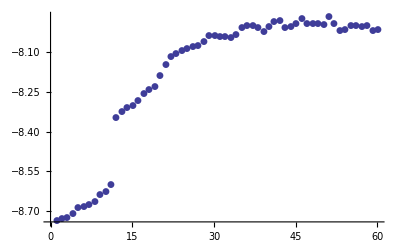

```mathematica
ListPlot[Transpose[res][[1]],PlotMarkers->Automatic]
```

```mathematica
Mean[est={-8.0261,-8.0320,-8.0296,-8.0272,-8.0314}]
StandardDeviation[est]/√(5-1)
```

-8.02926

0.0012853

```mathematica
τ=0.025; S=moni=Table[0,{n}]; res={}; L=Exp[-2 τ^(3/2)];
Do[Rn= Ro+τ Fo+Partition[RandomReal[NormalDistribution[0,√τ],12n],n];
Pn=Ψ/.Subscript[x, i_]:>Rn[[i]]; Fn=F/.Subscript[x, i_]:>Rn[[i]]; En=EL/.Subscript[x, i_]:>Rn[[i]];
T=Thread[Thread[10<moni]||Thread[ RandomReal[{0,1},n]<
Pn^2/Po^2 Exp[Sum[(Fo+Fn)[[i]](Ro-Rn+τ/2(Fo-Fn))[[i]],{i,12}]]]];
Ro=MapThread[If,{Table[T,{12}],Rn,Ro},2];
Fo=MapThread[If,{Table[T,{12}],Fn,Fo},2];
Eo=MapThread[If,{T,En,Eo}]; Po=MapThread[If,{T,Pn,Po}];
moni=MapThread[If,{T,Table[0,{n}],moni+1}];
Eh=Table[Min[Max[-0.5-0.03/τ,Eo[[i]]+8.03],0.5+0.03/τ],{i,n}];
S=S L + Eh; W=1 - τ S; W=W/Total[W];
res=Append[res,{Total[W Eo], Count[T,True]/n//N}],
{7000}]
```

$Aborted

```mathematica
r025=Drop[Map[Total,Partition[Transpose[res][[1]],1000]]/1000,1]
```

```mathematica
r025={-8.0675,-8.0666,-8.0676,-8.0662,-8.0668,-8.0669};
r050={-8.0722,-8.0728,-8.0727,-8.0736,-8.0741,-8.0723};
r075={-8.0815,-8.0799,-8.0818,-8.0778,-8.0795,-8.0813};
```

```mathematica
r025={-8.0675,-8.0666,-8.0676,-8.0662,-8.0668,-8.0669};
r050={-8.0722,-8.0728,-8.0727,-8.0736,-8.0741,-8.0723};
r075={-8.0815,-8.0799,-8.0818,-8.0778,-8.0795,-8.0813};
```

```mathematica
Show[ListPlot[reg,PlotRange->{{0,.08},{-8.084,-8.062}}],
Plot[-8.06225 -0.160667 q -1.06667 q^2, {q,0,.11}]]
```